## Installations

### Initializations

```mathematica
Clear["Global`*"]
Needs["SymbolicC`"];
targetDir=NotebookDirectory[];
SetDirectory[targetDir];
```

### Install Packages: DoublePendulum.

```mathematica
MyPackageDirectory=ToFileName[{ParentDirectory[ParentDirectory[]],"Packages"}]
```

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/4-Artikulurako-I/C-inplementazioa/Packages/

```mathematica
Get["DoublePendulum`",Path->MyPackageDirectory];
Get["MyFunctions`",Path->MyPackageDirectory];
```

DoublePendulumHam2::shdw: Symbol DoublePendulumHam2 appears in multiple contexts {DoublePendulum`,Global`}; definitions in context DoublePendulum` may shadow or be shadowed by other definitions.

### Plot Style

```mathematica
StyleQuad=Red;
StyleIdeal=Black;
StyleMachine=Lighter[Blue,.6];
StyleClassic=Lighter[Gray,.6];
StyleError=Black;
StyleEstimation=Lighter[Blue,.6];
MarkerQuad="○"; (*○  △    □*)
MarkerIdeal="▲"; (*●  ▲  ■*)
MarkerMachine="■";
```

## Filenames

```mathematica
DataDirectory="Data/";
ImagesDirectory="Images/";
```

```mathematica
filey0=NotebookDirectory[]<>DataDirectory<>"Datay0.bin";
fileA=NotebookDirectory[]<>DataDirectory<>"outA.bin";
fileB=NotebookDirectory[]<>DataDirectory<>"outB.bin";
fileC=NotebookDirectory[]<>DataDirectory<>"outC.bin";
fileD=NotebookDirectory[]<>DataDirectory<>"outD.bin";
```

## Parameters (non-chaotic initial values)

### Problem parameters and initial values.

```mathematica
prec=100;
n=2;
g=98/10;
m1=1;m2=1;
l1=1;l2=1;

C1=l2^2*m2;
C2=l1^2(m1+m2);
C3=-2 l1 l2 l2;
C4=2l1^2l2^2*m2*m1;
C5=2m1^2l2^2*m2^2;
C6=g l1 (m1+m2);
C7=g l2 m2;

Q10=(11/10);Q20=0;
P10=0;P20=27746/10000;
u0={Q10,Q20,P10,P20};
u0D= N[{Q10,Q20,P10,P20}];
u0DD=SetPrecision[u0D,prec];
ee0 =u0 - u0DD;

preal=parameters={C1,C2,C3,C4,C5,C6,C7};
pint={0,0};
```

```mathematica
u0
```

{11/10,0,0,13873/5000}

```mathematica
parameters
```

{1,2,-2,2,2,98/5,49/5}

```mathematica
stru0=ExportString[u0,"Real128"];
stre0 = ExportString[u0*0.0,"Real128"];
strrpar = ExportString[preal, "Real128"];
```

```mathematica
u0
```

{11/10,0,0,13873/5000}

```mathematica
N[ee0,20]
```

{-8.8817841970012523234×10^-17,0,0,4.476419235288631171×10^-17}

### Integration parameters.

```mathematica
t0=0.;tend=2.^(12) ;(*2.^(10)*)
tend=2.^(4);
h=2.^(-7);
sampling=2^7; (*2^7*)
sampling=1;
```

```mathematica
codfun0=1; (*OdePendulum*)
codfunX=11; (*OdePendulumX*)
approx = 1; 
ns= 6;
nstep=(tend-t0)/h;
nout=nstep/sampling
```

2048.

### RKG parameters

```mathematica
neq=4;
prec=100;
HAM=DoublePendulumHam2;
```

## Analisis-I

### Import and mean

```mathematica
noutA=Round[nout]+1;
nstat=100; 
step=4;
dd1= (2neq+1);
dd2= (3neq+1);
```

```mathematica
outA=SetPrecision[ArrayReshape[BinaryReadList[fileA,"Real128"],{nstat,noutA,dd1}],prec];
outB=SetPrecision[ArrayReshape[BinaryReadList[fileB,"Real128"],{nstat,noutA,dd1}],prec];
outC=SetPrecision[ArrayReshape[BinaryReadList[fileC,"Real64"],{nstat,noutA,dd2}],prec];
outD=SetPrecision[ArrayReshape[BinaryReadList[fileD,"Real64"],{nstat,noutA,dd1}],prec];
tpA=Flatten[Take[outA[[1]],All,{1,1}]];
tpA=Map[First,Partition[tpA,step]];
tpB=Flatten[Take[outB[[1]],All,{1,1}]];
tpB=Map[First,Partition[tpB,step]];
tpC=Flatten[Take[outC[[1]],All,{1,1}]];
tpC=Map[First,Partition[tpC,step]];
tpD=Flatten[Take[outD[[1]],All,{1,1}]];
tpD=Map[First,Partition[tpD,step]];
```

```mathematica
{Length[outA],Length[outA[[1]]]}
```

{100,2049}

```mathematica
{Length[outB],Length[outB[[1]]]}
```

{100,2049}

```mathematica
{Length[outC],Length[outC[[1]]]}
```

{100,2049}

```mathematica
{Length[outD],Length[outD[[1]]]}
```

{100,2049}

```mathematica
{MeanHamA,DesvHamA,MeanErrA,EndHamA}=FunMeanHerr[outA,outA, nstat,noutA,HAM, parameters,neq,prec,step] ;
{MeanHamB,DesvHamB,MeanErrB,EndHamB}=FunMeanHerr[outB,outA, nstat,noutA,HAM, parameters,neq,prec,step] ;
{MeanHamC,DesvHamC,MeanErrC, EndHamC}=FunMeanHerr[outC,outA, nstat,noutA,HAM, parameters,neq,prec,step] ;
{MeanHamD,DesvHamD,MeanErrD, EndHamD}=FunMeanHerr[outD,outA, nstat,noutA,HAM, parameters,neq,prec,step] ;
```

```mathematica
HamerrA=FunHerr[outA,nstat,noutA,HAM, parameters,neq,prec,step] ;
HamerrB=FunHerr[outB,nstat,noutA,HAM, parameters,neq,prec,step] ;
HamerrC=FunHerr[outC,nstat,noutA,HAM, parameters,neq,prec,step] ;
HamerrD=FunHerr[outD,nstat,noutA,HAM, parameters,neq,prec,step] ;
```

### Graphics-I (Energy)

```mathematica
MeanHamAdata = Transpose[{tpA,MeanHamA}];
MeanHamBdata = Transpose[{tpB,MeanHamB}];
MeanHamCdata = Transpose[{tpC,MeanHamC}];
MeanHamDdata = Transpose[{tpD,MeanHamD}];
DesvHamAdata = Transpose[{tpA,DesvHamA}];
DesvHamBdata = Transpose[{tpB,DesvHamB}];
DesvHamCdata = Transpose[{tpC,DesvHamC}];
DesvHamDdata = Transpose[{tpD,DesvHamD}];
```

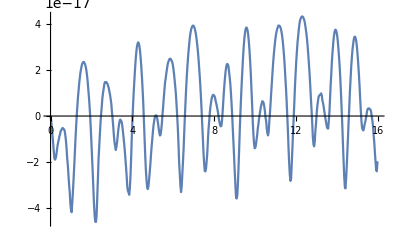

```mathematica
ListPlot[{MeanHamBdata},Joined->True]
```

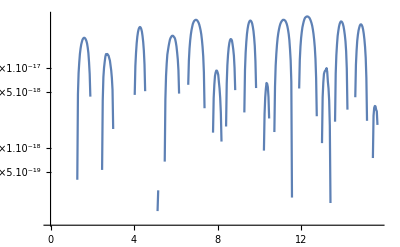

```mathematica
ListLogPlot[{MeanHamBdata},Joined->True]
```

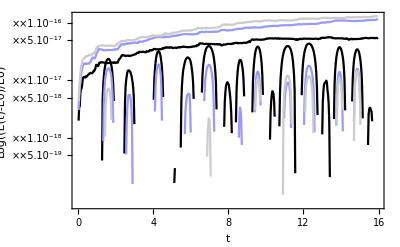

```mathematica
plot=ListLogPlot[{MeanHamBdata,MeanHamCdata,MeanHamDdata,DesvHamBdata,DesvHamCdata,DesvHamDdata},AxesLabel->{"t","Log((E(t)-E0)/E0)"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
PlotStyle->{StyleIdeal,StyleMachine,StyleClassic},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Log((E(t)-E0)/E0)"}]
Export[NotebookDirectory[]<>ImagesDirectory<>"plot3a.pdf",Show[plot] ];
```

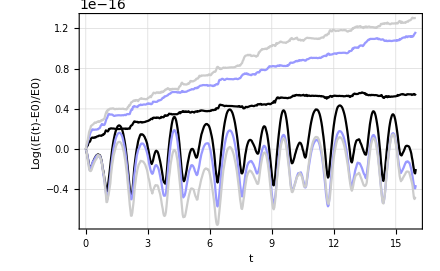

```mathematica
plot=ListPlot[{MeanHamBdata,MeanHamCdata,MeanHamDdata,DesvHamBdata,DesvHamCdata,DesvHamDdata},AxesLabel->{"t","Log((E(t)-E0)/E0)"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
PlotStyle->{StyleIdeal,StyleMachine,StyleClassic},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Log((E(t)-E0)/E0)"}]
Export[NotebookDirectory[]<>ImagesDirectory<>"plot3a-2.pdf",Show[plot] ];
```

### Graphics-I (Energy-2)

```mathematica
AllHamerrB=FunAllHerr[outB, nstat,noutA,HAM, parameters,neq,prec,step] ;
AllHamerrC=FunAllHerr[outC, nstat,noutA,HAM, parameters,neq,prec,step] ;
AllHamerrD=FunAllHerr[outD, nstat,noutA,HAM, parameters,neq,prec,step] ;
```

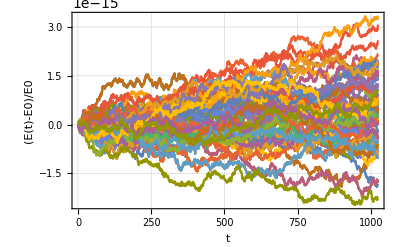

```mathematica
plot=ListPlot[Table[AllHamerrB[[i]],{i,nstat}],AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
```

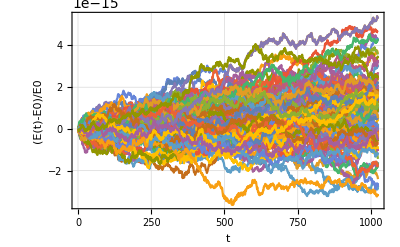

```mathematica
plot=ListPlot[Table[AllHamerrC[[i]],{i,nstat}],AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
Export[NotebookDirectory[]<>ImagesDirectory<>"plotHamC-1.pdf",Show[plot] ];
```

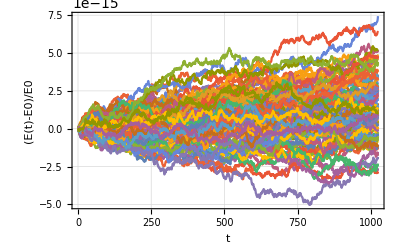

```mathematica
plot=ListPlot[Table[AllHamerrD[[i]],{i,nstat}],AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
```

### Graphics-II (Global Error)

```mathematica
MeanErrAdata = Transpose[{tpA,MeanErrA}];
MeanErrBdata = Transpose[{tpB,MeanErrB}];
MeanErrCdata = Transpose[{tpC,MeanErrC}];
MeanErrDdata = Transpose[{tpD,MeanErrD}];
```

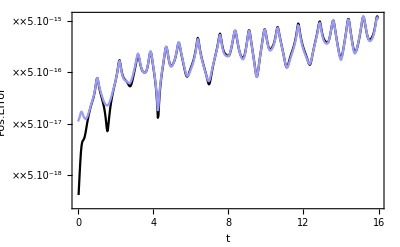

```mathematica
plot=ListLogPlot[{MeanErrBdata,MeanErrCdata(*,MeanErrDdata*)},AxesLabel->{"t","Pos.Error"},Joined->True,PlotRange->All,
(*PlotLegends->Placed[{"ideal","rdigits=0"(*,"rdigits=3"*)},Below],*)
(*PlotRange->Automatic,*)
PlotTheme->"Detailed",
PlotStyle->{StyleIdeal,StyleMachine,StyleClassic},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Pos.Error"}]
Export[NotebookDirectory[]<>ImagesDirectory<>"plot3b.pdf",Show[plot] ];
```

### Graphics-III (Histogram)

#### Ideal

-0.0003863923591157846720180235482885696350593305042456059307565828473073701412184523

0.0482253897404168953841810324963760073711858752530852110979814020357816843024785936

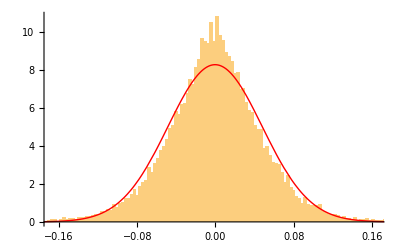

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/4-Artikulurako-I/C-inplementazioa/Experiments/DoublePendulum (NonChaotic k6)/Images/brouwer4a.pdf

```mathematica
Hamerdif=HamerrB 10^16;
μ=Mean[Hamerdif]
σ=StandardDeviation[Hamerdif]
ir1=Histogram[Hamerdif,{σ/16},"PDF"];
ir2=Plot[PDF[NormalDistribution[μ,σ],x],{x,-16*σ,16*σ},PlotStyle->{Red,Thick},PlotRange->All,WorkingPrecision->prec];
Show[ir1,ir2]
Export[NotebookDirectory[]<>ImagesDirectory<>"brouwer4a.pdf",Show[ir1,ir2]]
```

```mathematica
Length[Hamerdif]
```

51100

#### Machine precision (rdigits=0)

-0.00007006148845770893241685403489653961871239292874906626703922657678623556071516641

0.00610844363891009747152677442183576370536912461562121207696376475978930230656477566

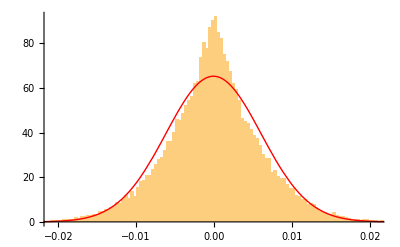

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/4-Artikulurako-I/C-inplementazioa/Experiments/DoublePendulum (NonChaotic k6)/Images/brouwer4b.pdf

```mathematica
Hamerdif=HamerrC 10^15;
μ=Mean[Hamerdif]
σ=StandardDeviation[Hamerdif]
ir1=Histogram[Hamerdif,{σ/16},"PDF"];
ir2=Plot[PDF[NormalDistribution[μ,σ],x],{x,-16*σ,16*σ},PlotStyle->{Red,Thick},PlotRange->All,WorkingPrecision->prec];
Show[ir1,ir2]
Export[NotebookDirectory[]<>ImagesDirectory<>"brouwer4b.pdf",Show[ir1,ir2]]
```

### Tables

#### Quadruple

```mathematica
MeanD0=0.; (*(SD0A/nstat)/steps*100;*)
MaxDE=Max[MeanHamA]//N;
Hamerdif=Drop[MeanHamA ,1]-Drop[ MeanHamA,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
Gerror=Max[MeanErrA]//N;
{N[MeanD0],MaxDE,μ,σ,Gerror}
```

{0.,1.93479×10^-19,-2.17377×10^-24,1.58572×10^-20,0.}

#### Ideal

```mathematica
MeanD0=0.;(*(SD0B/nstat)/steps*100;*)
MaxDE=Max[MeanHamB]//N;
Hamerdif=Drop[MeanHamB ,1]-Drop[ MeanHamB,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
Gerror=Max[MeanErrB]//N;
{N[MeanD0],MaxDE,μ,σ,Gerror}
```

{0.,4.34145×10^-17,-3.86392×10^-20,3.73993×10^-18,6.08086×10^-15}

#### Machine

```mathematica
MeanD0=0.;(*(SD0C/nstat)/steps*100;*)
MaxDE=Max[MeanHamC]//N;
Hamerdif=Drop[MeanHamC ,1]-Drop[ MeanHamC,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
Gerror=Max[MeanErrC]//N;
{N[MeanD0],MaxDE,μ,σ,Gerror}
```

{0.,1.89737×10^-17,-7.00615×10^-20,3.74455×10^-18,6.13187×10^-15}

#### Machine Classic

```mathematica
MeanD0=0.;(*(SD0C/nstat)/steps*100;*)
MaxDE=Max[MeanHamD]//N;
Hamerdif=Drop[MeanHamD ,1]-Drop[ MeanHamD,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
Gerror=Max[MeanErrD]//N;
{N[MeanD0],MaxDE,μ,σ,Gerror}
```

{0.,1.46851×10^-17,-9.31999×10^-20,3.76013×10^-18,6.62785×10^-15}

## Analisis-II: error estimation

### Estimation

```mathematica
MeanErrCdata = Transpose[{tpC,MeanErrC}];
```

```mathematica
{MeanEstC,DesvEstC,MeanQtyC,DesvQtyC}=FunMeanEst[outC,outA,nstat,noutA,neq,prec,step];
```

```mathematica
MeanEstCdata = Transpose[{tpC,MeanEstC}];
DesvdataC1=Transpose[{tpC,MeanEstC+DesvEstC}];
DesvdataC2=Transpose[{tpC,MeanEstC-DesvEstC}];
```

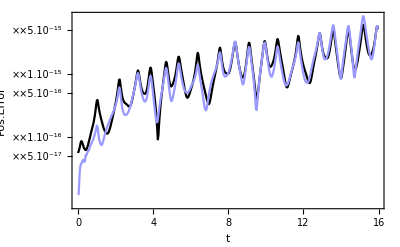

```mathematica
plot=ListLogPlot[{Abs[MeanErrCdata],Abs[MeanEstCdata]},AxesLabel->{"t","Pos.Error"},Joined->True,
(*PlotRange->All*)
(*PlotLegends->Placed[{"Error","Estimation-par","Estimation-seq"},After],*)
PlotTheme->"Detailed",
PlotStyle->{StyleError,StyleEstimation},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Pos.Error"}]
Export[NotebookDirectory[]<>ImagesDirectory<>"plot5a.pdf",Show[plot]];
```

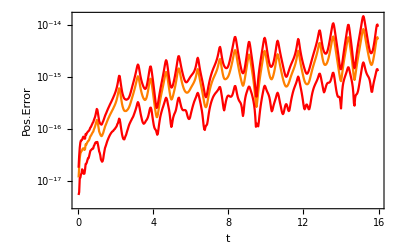

```mathematica
plot6b=ListLogPlot[{ MeanEstCdata,
                                          DesvdataC1,DesvdataC2},
AxesLabel->{"t","Pos.Error"},Joined->True,
(*PlotRange->All*)
(*PlotLegends->Placed[{"Error","Estimation-par","Estimation-seq"},After],*)
PlotTheme->"Detailed",
PlotStyle->{Orange,Red,Red},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Pos.Error"}]
```

### Quality estimation

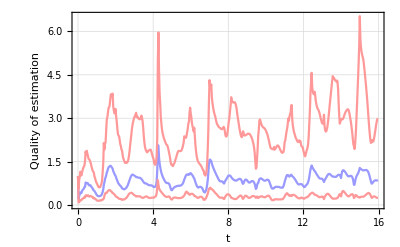

```mathematica
MeanQtyCdata=Transpose[{tpC,10^MeanQtyC}];
MeanQtyCData1=Transpose[{tpC,10^(MeanQtyC+DesvQtyC)}];
MeanQtyCData2=Transpose[{tpC,10^(MeanQtyC-DesvQtyC)}];
plot=ListPlot[{MeanQtyCdata,MeanQtyCData1,MeanQtyCData2},AxesLabel->{"t","|Err_Est|/|Err|"},Joined->True,
PlotRange->All,
PlotTheme->"Detailed",
PlotStyle->{StyleEstimation,Lighter[Red,.6],Lighter[Red,.6]},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Quality of estimation"}]
Export[NotebookDirectory[]<>ImagesDirectory<>"plot5b.pdf",Show[plot]];
```

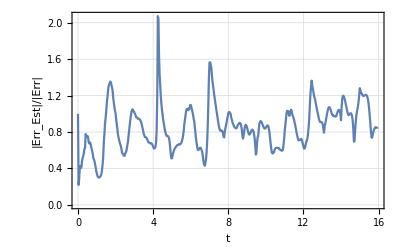

```mathematica
plot=ListPlot[{MeanQtyCdata},AxesLabel->{"t","|Err_Est|/|Err|"},Joined->True,
PlotRange->All,
PlotTheme->"Detailed",
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","|Err_Est|/|Err|"}]
```